Block Encoding |

Block Encodingpaclet:Q3/tutorial/BlockEncoding#1159336212 | Examplespaclet:Q3/tutorial/BlockEncoding#4935158
Notespaclet:Q3/tutorial/BlockEncoding#1815688453 |

Block encoding is a method to get a quantum computer accessible to the information in a matrix M. Typically, the resulting bigger embedding matrix is denoted by U_M and has the block form

U_M:=(M | *
* | *) ,

where * indicates the corresponding block is irrelevant.

BlockEncodingpaclet:Q3/ref/BlockEncodingQ3 Package Symbol | Implements a block encoding of a matrix
UniformlyControlledGatepaclet:Q3/ref/UniformlyControlledGateQ3 Package Symbol | Uniformly controlled unitary gates

Q3 functions related to an implementation of block encoding.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Block Encoding

Let M be a N×N (with N:=2^n) complex matrix, which is not unitary in general. Suppose that M has the singular-value decomposition M=VΛ W^†, where V and W are unitary matrices and Λ:=diagonal(λ_1,λ_2,…,λ_N)≥0 is the diagonal matrix of singular values. We assume that the singular values are all less than 1; 0≤λ_k≤1. Note that this is not a restriction since one can always rescale the matrix by a constant factor.

In Q3, the block encoding is implemented as

M↦U_M:=(V | 0
0 | V)(Λ | √(1-Λ^2)
√(1-Λ^2) | -Λ)(W^† | 0
0 | W^†) .

For a quantum circuit model of this implementation, we introduce a rotated basis state

θ:=R_y(θ)0≐(cos(θ/2)
sin(θ/2))

and the reflection in the line along the vector θ (see also Figure 2 for a geometric interpretation)

Ω_θ:=2θθ-1=R_y(θ)ZR_y^†(θ)≐(cosθ | sinθ
sinθ | -cosθ),

and note that

(λ | √(1-λ^2)
√(1-λ^2) | -λ)≐Ω_θ

with cosθ:=λ (i.e., sinθ=√(1-λ^2)). Then, the block encoding U_M can be rewritten as

U_M=(I⊗V)(Σ_k Ω_θ_k⊗kk)(I⊗W^†),

where cos θ_k:=λ_k and {k:k=0,1,…,2^n-1} is the computational basis of the system register. In particular, the expression Σ_k Ω_θ_k⊗kk in the middle is nothing but the uniformly-controlled unitary gate operating Ω_θ_kconditioned on the state k of the system register.

Putting all together, the block encoding U_M may be described by the quantum circuit in Figure 1.

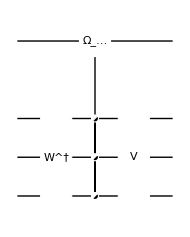
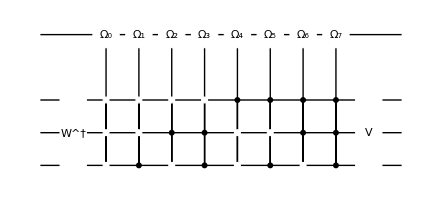
=-Graphics-=-Graphics-

Figure 1. Equivalent quantum circuits representing the block encoding of matrix M that has singular value decomposition M=VΛ W^† with Λ:=diag(λ_1,λ_2,,…,λ_n). Here, Ω_k:=Ω_θ_k and cos(θ_k):=λ_k.

As one can see in Figure 1, the computational cost of block encoding is exponentially high in general.

Notes

### Alternative Block Encoding

Another common implementation of block encoding is through the mapping [see, e.g., Lin (2022)]

M↦(V | 0
0 | I)(Λ | √(1-Λ^2)
√(1-Λ^2) | -Λ)(W^† | 0
0 | I) .

Q3 does not consider this because (V | 0
0 | I) and (W^† | 0
0 | I) correspond to controlled-unitary gates. When V and W are large, the actual implementation of those controlled-unitary gates may be computationally expensive.

### Relation to the Grover Rotation

The reflection Ω_θ in the line along the vector θ can be converted to the rotation around the y-axis by angle 2θ by multiplying the Pauli Z operator; that is,

Ω_θ Z=R_y(θ)ZR_y^†(θ)Z=R_y(θ)R_y(θ)=R_y(2θ)≐(cosθ | -sinθ
sinθ | cosθ) .

This relation can also be understood with a geometrical view as shown in Figure 2. The Grover rotation in quantum search algorithm has also a similar geometric interpretation.

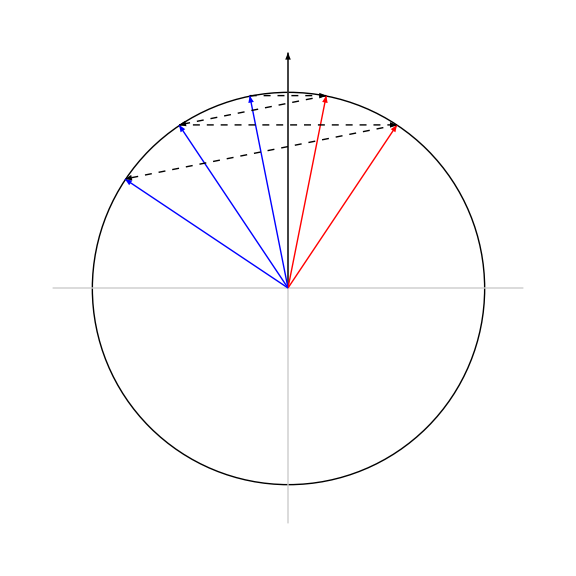

Figure 2. A geometric view of the effects of the reflection Z in the line along the computational basis vector 0 and the reflection Ω_θ in the line along the rotated basis vector θ:=R_y(θ)0. Shown is the zx-plane in the Bloch space with the z-axis in the vertical direction and the y-axis pointing out of the screen.

Examples

See the documentation for BlockEncoding.

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Computation: Overview
▪Quantum Information Systems with Q3

| Related Links
▪A. Gilyen, Y. Su, G. Hao, and N. Wiebe (2019)https://doi.org/10.1145/3313276.3316366, Proceedings of the 51st Annual ACM SIGACT Symposium on Theory of Computing, "Quantum singular value transformation and beyond: exponential improvements for quantum matrix arithmetics."
▪L. Lin (2022)https://arxiv.org/abs/2201.08309, arXiv:2201.08309, "Lecture Notes on Quantum Algorithms for Scientific Computation."
▪J. M. Martyn, Z. M. Rossi, A. K. Tan, I. L. Chuan (2021)https://doi.org/10.1103%2Fprxquantum.2.040203, PRX Quantum 2, 4 040203, "Grand Unification of Quantum Algorithms."
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).